```mathematica
(*parameters = Import["/Users/cadenlin/Downloads/SCC COVID .xlsx",{"Data",2,42}];
paramquarantineforall=parameters[[1]];
sdistance=parameters[[2]];
rateinf=parameters[[3]]
popinfnow=parameters[[6]];
poprec=parameters[[7]];*)
rateasym = 0.31;
ratedeath=1;
raterecasym = 1/14;
raterecsym = 1/19;
rateinc=1/5.7;
ratequar=1.75;
(*poppos=popinfnow*rateasym;
popquar=popinfnow-poppos;
popasym = popinfnow*2;
popinc=popasym*3/14;
popsusc=1-popasym-popinc-poppos-popquar-poprec;*)
poptotal = 1928000;
sstart1=1-istart1-astart1-pstart1-qstart1-rstart1-dstart1;
istart1=0.000001;
astart1=0.000001;
pstart1=7.78008*10^-6*rateasym;
qstart1=7.78008*10^-6-pstart1;
rstart1=0.012181305-0.003334025;
dstart1=0.000001556;
```

```mathematica
(*currentcasedata=Import["/Users/cadenlin/Downloads/SCC COVID .xlsx",{"Data",3}];
currentdeathdata=Import["/Users/cadenlin/Downloads/SCC COVID .xlsx",{"Data",7}];
updatedcurrentcasedata=Import["/Users/cadenlin/Downloads/SCC Covid Updated Xmas.xlsx",{"Data",2}];
```

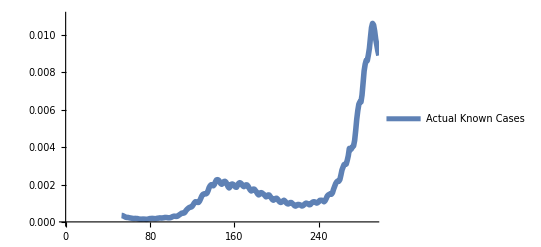

```mathematica
(*actualcaseplot=ListPlot[currentcasedata,PlotLegends->{"Actual Known Cases"},Joined->True,PlotStyle-> Thickness[0.01]];
actualdeathplot=ListPlot[currentdeathdata,PlotLegends->{"Actual Known Deaths"},Joined->True,PlotStyle -> Thickness[0.01]];
updatedactualcaseplot=ListPlot[updatedcurrentcasedata,PlotLegends->{"Actual Known Cases"},Joined->True,PlotStyle-> Thickness[0.01],PlotRange->{{0,291},{0,0.011}}]
```

```mathematica
days1=0;
daysshift=0;
infectionrate1[t_]=(0.4645*E^(-0.0610t));
infectionrate2[t_]=0.00135702t-0.03865422;
infectionrate3[t_]=0.00008619t^2-0.02403308t+1.75188688;
infectionrate4[t_]=-0.00009458t+0.06901033;
infectionrate5[t_]=0.00065791t-0.08143686;
infectionrate[t_]=Piecewise[{{infectionrate1[t],0<=t≤43+days1},{infectionrate2[t], 43+days1<t≤113},{infectionrate3[t], 113<t≤143},{infectionrate4[t], 143<t≤213},{infectionrate5[t],213<t}}];
infectionrateshifted[t_]=Piecewise[{{infectionrate1[t],0<=t≤43+daysshift},{infectionrate2[t], 43+daysshift<t≤113+daysshift},{infectionrate3[t], 113+daysshift<t≤143+daysshift},{infectionrate4[t], 143+daysshift<t≤213+daysshift},{infectionrate5[t],280≥ t>213+daysshift},{infectionrate4[t],t>280}}];
```

```mathematica
(*0,43,113,143,213,275*)
```

```mathematica
deathrate[t_]=Piecewise[{{0.004,0≤t≤70},{0.00062,t>70}}];
```

```mathematica
vaccinerate1[t_]=Piecewise[{{ρ*θ,t>280}}];
```

```mathematica
testingrate1[t_]=(9.0525*E^(0.2574t))/poptotal;
testingrate2[t_]=(-0.034853t^3+5.162249t^2-213.236023t+3156.424255)/poptotal;
testingrate3[t_]=(9069.32*Log[t]-37864.8)/poptotal;
testingrate4[t_]=(7.8545t+4819.2)/poptotal;
testingrate5[t_]=(76.876t-8834.6)/poptotal;
testingrate[t_]=Piecewise[{{testingrate1[t],0<=t≤18},{testingrate2[t],18<t≤74},{testingrate3[t],74<t≤138},{testingrate4[t],138<t≤216},{testingrate5[t],216<t}}];
```

```mathematica
saqprdv778={{s'[t]==-(infectionrate[t]/χ) s[t] *q[t]-infectionrate[t]s[t] a[t]/ζ- (infectionrate[t]/χ)*s[t]*p[t]-infectionrate[t] s[t] i[t]/ζ-vaccinerate1[t]*s[t],
i'[t]==(infectionrate[t]/χ) s[t] *q[t]+infectionrate[t] s[t] a[t]/ζ+ (infectionrate[t]/χ)*s[t]*p[t]+infectionrate[t] s[t] i[t]/ζ-λ*i[t]-(testingrate[t]*ω)*i[t],
a'[t]==α*λ*i[t]-(testingrate[t]*ω)*a[t]-γ1*a[t],
q'[t]==(1-α)(λ)(i[t])-γ2 *q[t]-deathrate[t]*δ *q[t],
p'[t]==(testingrate[t]*ω)*a[t]+(testingrate[t]*ω)*i[t]-γ1*p[t],
r'[t]==γ1 (a[t]+p[t])+γ2(q[t]),
d'[t]==deathrate[t]*δ*q[t],
v'[t]==vaccinerate1[t]*s[t] },
s[0]==sstart1,i[0]==istart1,a[0]==astart1,q[0]==qstart1,p[0]==pstart1,r[0]==rstart1,v[0]==0,d[0]==dstart1};
```

```mathematica
saqprdvbetashifted778={{s'[t]==-(infectionrateshifted[t]/χ) s[t] *q[t]-infectionrateshifted[t]s[t] a[t]/ζ- (infectionrateshifted[t]/χ)*s[t]*p[t]-infectionrateshifted[t] s[t] i[t]/ζ-vaccinerate1[t]*s[t],
i'[t]==(infectionrateshifted[t]/χ) s[t] *q[t]+infectionrateshifted[t] s[t] a[t]/ζ+ (infectionrateshifted[t]/χ)*s[t]*p[t]+infectionrateshifted[t] s[t] i[t]/ζ-λ*i[t]-(testingrate[t]*ω)*i[t],
a'[t]==α*λ*i[t]-(testingrate[t]*ω)*a[t]-γ1*a[t],
q'[t]==(1-α)(λ)(i[t])-γ2 *q[t]-deathrate[t]*δ *q[t],
p'[t]==(testingrate[t]*ω)*a[t]+(testingrate[t]*ω)*i[t]-γ1*p[t],
r'[t]==γ1 (a[t]+p[t])+γ2(q[t]),
d'[t]==deathrate[t]*δ*q[t],
v'[t]==vaccinerate1[t]*s[t] },
s[0]==sstart1,i[0]==istart1,a[0]==astart1,q[0]==qstart1,p[0]==pstart1,r[0]==rstart1,v[0]==0,d[0]==dstart1};
```

```mathematica
parfun778=ParametricNDSolveValue[saqprdv778,{s,i,a,q,p,r,d,v},{t,0,550},{γ1,γ2,χ,θ,ρ,δ,ζ,α,λ,ω}];
parfunInfect778=ParametricNDSolveValue[saqprdv778,{i,a,q,p,d},{t,0,550},{γ1,γ2,χ,θ,ρ,δ,ζ,α,λ,ω}];parfunRecover778=ParametricNDSolveValue[saqprdv778,{r},{t,0,280},{γ1,γ2,χ,θ,ρ,δ,ζ,α,λ,ω}];
parfunKnown=ParametricNDSolveValue[saqprdv778,{p,q,a},{t,0,300},{γ1,γ2,χ,θ,ρ,δ,ζ,α,λ,ω}];
parfunDead=ParametricNDSolveValue[saqprdv778,{d},{t,0,280},{γ1,γ2,χ,θ,ρ,δ,ζ,α,λ,ω}];
parfunRecBetaOne=ParametricNDSolveValue[saqprdvbetashifted778,{r},{t,0,280},{γ1,γ2,χ,θ,ρ,δ,ζ,α,λ,ω}];
parfunDeadBetaOne=ParametricNDSolveValue[saqprdvbetashifted778,{d},{t,0,280},{γ1,γ2,χ,θ,ρ,δ,ζ,α,λ,ω}];
```

```mathematica
Manipulate[GraphicsColumn[{Show[Plot[Evaluate@Through[parfunKnown[γ1,γ2,χ,θ,ρ,δ,ζ,α,λ,ω][t]],{t,0,300},PlotLegends->{"Predicted Known Asymtomatic Cases ","Predicted Known Symptomatic Cases","Predicted Unknown Asymptomatic Cases","Tested Positive(Quarantined)","Dead"},TicksStyle -> Large,AxesLabel->{Style["Days After 3/2",Black,FontSize->16],Style["Fraction of Population",Black,FontSize->16]},PlotStyle->{{Darker[Green],Thickness[0.01]},{Red,Thickness[0.01]},{Magenta,Thickness[0.01]}},ImageSize->Large,PlotRange->All](*,updatedactualcaseplot*),PlotRange  -> {{0,300},{0,0.011}}],
Show[Plot[Evaluate@Through[parfunDead[γ1,γ2,χ,θ,ρ,δ,ζ,α,λ,ω][t]],{t,0,280},TicksStyle -> Large,PlotLegends->{"Predicted Deaths"},AxesLabel->{Style["Days After 3/2",Black,FontSize->16],Style["Fraction of Population",Black,FontSize->16]},PlotStyle->{Orange,Thickness[0.01]},ImageSize->Large](*,actualdeathplot*)],
Plot[Evaluate@Through[parfunInfect778[γ1,γ2,χ,θ,ρ,δ,ζ,α,λ,ω][t]],{t,0,550},PlotLegends->{"Incubation","Asymptomatic","Symptomatic(Quarantined)","Tested Positive(Quarantined)","Dead"},TicksStyle->Large,AxesLabel->{Style["Days After 3/2",Black,FontSize->16],Style["Fraction of Population",Black,FontSize->16]},PlotStyle->{{Red,Thickness[0.007]},{Orange,Thickness[0.007]},{Magenta,Thickness[0.007]},{Darker[Green],Thickness[0.007]},{Blue,Thickness[0.007]},{Purple,Thickness[0.007]}, {Cyan,Thickness[0.007]}, {Black,Thickness[0.007]}},ImageSize->Large,PlotRange->{{250,550},{0,0.15}}],
Show[Plot[Evaluate@Through[parfunRecover778[γ1,γ2,χ,θ,ρ,δ,ζ,α,λ,ω][t]],{t,0,280},PlotLegends->{"Recovered Normal"},TicksStyle -> Large,AxesLabel->{Style["Days After 3/2",Black,FontSize->16],Style["Fraction of Population",Black,FontSize->16]},PlotStyle->{Orange,Thickness[0.01]},ImageSize->Large],Plot[Evaluate@Through[parfunRecBetaOne[γ1,γ2,χ,θ,ρ,δ,ζ,α,λ,ω][t]],{t,0,280},PlotLegends->{"Recovered Normal"},TicksStyle -> Large,AxesLabel->{Style["Days After 3/2",Black,FontSize->16],Style["Fraction of Population",Black,FontSize->16]},PlotStyle->{Blue,Thickness[0.01]},ImageSize->Large],PlotRange  -> All],
Show[Plot[Evaluate@Through[parfunDead[γ1,γ2,χ,θ,ρ,δ,ζ,α,λ,ω][t]],{t,0,280},PlotLegends->{"Dead Normal"},TicksStyle -> Large,AxesLabel->{Style["Days After 3/2",Black,FontSize->16],Style["Fraction of Population",Black,FontSize->16]},PlotStyle->{Orange,Thickness[0.01]},ImageSize->Large],Plot[Evaluate@Through[parfunDeadBetaOne[γ1,γ2,χ,θ,ρ,δ,ζ,α,λ,ω][t]],{t,0,280},PlotLegends->{"Dead good"},TicksStyle -> Large,AxesLabel->{Style["Days After 3/2",Black,FontSize->16],Style["Fraction of Population",Black,FontSize->16]},PlotStyle->{Blue,Thickness[0.01]},ImageSize->Large],PlotRange  -> All]
},
ImageSize->Full],
{{γ1,raterecasym,"Recovery rate (asymptomatic)"},0,0.3,Appearance->"Labeled"},
{{γ2,raterecsym,"Recovery rate (symptomatic)"},0,0.3,Appearance->"Labeled"},
{{χ,ratequar,"Quarantine effect for known infections"},1,100,Appearance->"Labeled"},
{{θ,0,"Vaccination availability"},0,0.02,Appearance->"Labeled"},
{{ρ,0.9,"Vaccine efficacy"},0,1,Appearance->"Labeled"},
{{δ,ratedeath,"Death rate"},0,2,Appearance->"Labeled"},
{{ζ,1,"Social distancing"},0,2,Appearance->"Labeled"},
{{α,rateasym,"Asymptomatic rate"},0,1,Appearance->"Labeled"},
{{λ,rateinc,"Incubation rate"},0,1,Appearance->"Labeled"},
{{ω,1,"Testing factor"},0,3,Appearance->"Labeled"}]
```

```mathematica
parfunSym=ParametricNDSolve[saqprdv778,{q},{t,0,600},{γ1,γ2,χ,θ,ρ,δ,ζ,α,λ,ω}];
parfunRec=ParametricNDSolve[saqprdv778,{r},{t,0,600},{γ1,γ2,χ,θ,ρ,δ,ζ,α,λ,ω}];
parfunDeath=ParametricNDSolve[saqprdv778,{d},{t,0,600},{γ1,γ2,χ,θ,ρ,δ,ζ,α,λ,ω}];
parfunPos=ParametricNDSolve[saqprdv778,{p},{t,0,600},{γ1,γ2,χ,θ,ρ,δ,ζ,α,λ,ω}];
parfunBetaOneRec=ParametricNDSolve[saqprdvbetashifted778,{r},{t,0,600},{γ1,γ2,χ,θ,ρ,δ,ζ,α,λ,ω}];
parfunBetaOneDead=ParametricNDSolve[saqprdvbetashifted778,{d},{t,0,600},{γ1,γ2,χ,θ,ρ,δ,ζ,α,λ,ω}];
```

```mathematica
socialdistancing=1;
ratequar=1.75;
ratetest=1;
vaccineavail=0.0;
rateinc=1/5.7;
rateasym=0.31;
texperiment=550;
posGraph=p[raterecasym,raterecsym,ratequar,vaccineavail,0.9,ratedeath,socialdistancing,rateasym,rateinc,ratetest]/.parfunPos;
symGraph=q[raterecasym,raterecsym,ratequar,vaccineavail,0.9,ratedeath,socialdistancing,rateasym,rateinc,ratetest]/.parfunSym;
recGraph=r[raterecasym,raterecsym,ratequar,vaccineavail,0.9,ratedeath,socialdistancing,rateasym,rateinc,ratetest]/.parfunRec;
deadGraph=d[raterecasym,
raterecsym,ratequar,vaccineavail,0.9,ratedeath,socialdistancing,rateasym,rateinc,ratetest]/.parfunDeath;
recGraphBetaOne=r[raterecasym,raterecsym,ratequar,vaccineavail,0.9,ratedeath,socialdistancing,rateasym,rateinc,ratetest]/.parfunBetaOneRec;
deadGraphBetaOne=d[raterecasym,
raterecsym,ratequar,vaccineavail,0.9,ratedeath,socialdistancing,rateasym,rateinc,ratetest]/.parfunBetaOneDead;

symGraph[300]+posGraph[300];
recGraph[texperiment]
deadGraph[texperiment]
recGraphBetaOne[texperiment];
deadGraphBetaOne[texperiment];
deadGraph[25];
```

0.903117

0.00693025

```mathematica
(*saqprdv777=
{{s'[t]==-(β/(χ(1+ζ*(p[t]+q[t])))) s[t] *q[t]-θ* s[t]-(β/(σ(1+ζ*(p[t]+q[t])))) s[t] a[t]- (β/(χ(1+ζ*(p[t]+q[t]))))*s[t]*p[t]-(β/(σ(1+ζ*(p[t]+q[t])))) s[t] i[t]+ρ*v[t],
i'[t]==(β/(χ(1+ζ*(p[t]+q[t])))) s[t] *q[t]+(β/(σ(1+ζ*(p[t]+q[t])))) s[t] a[t]+ (β/(χ(1+ζ*(p[t]+q[t]))))*s[t]*p[t]+(β/(σ(1+ζ*(p[t]+q[t])))) s[t] i[t]-λ*i[t]-ω*α*i[t],
a'[t]==α*λ*i[t]-ω*a[t]-γ1*a[t],
q'[t]==(1-α)(λ)(i[t])-γ2 *q[t]-δ *q[t],
p'[t]==ω*a[t]+ω*α*i[t]-γ1*p[t],
r'[t]==γ1 (a[t]+p[t])+γ2(q[t]),
d'[t]==δ*q[t],
v'[t]==θ*s[t]-ρ*v[t] },
s[0]==0.993,i[0]==0.005,a[0]==0.0005,q[0]==0.0005,p[0]==0.0005,r[0]==0.005,v[0]==0,d[0]==0}*)
```

```mathematica
(*parfun777=ParametricNDSolveValue[saqprdv777,{s,i,a,q,p,r,d,v},{t,0,500},{β,γ1,γ2,χ,θ,ρ,δ,ζ,ω,α,σ,λ}]
```

```mathematica
(*parfun777=ParametricNDSolveValue[saqprdv777,{s,i,a,q,p,r,d,v},{t,0,1000},{β,γ1,γ2,χ,θ,ρ,δ,ζ,ω,α,σ,λ}];
Manipulate[Plot[Evaluate@Through[parfun777[β,γ1,γ2,χ,θ,ρ,δ,ζ,ω,α,σ,λ][t]],{t,0,1000},PlotLegends->{"Susceptible","Incubation","Asymptomatic","Symptomatic(Quarantined)","Tested Positive(Quarantined)","Recovered","Dead","Vaccinated"},AxesLabel->{"Time","Fraction of Population"},PlotStyle->{Red,Orange,Magenta,Darker[Green],Blue,Purple, Cyan},ImageSize->Large,PlotRange->All],
{{β,parameters[[3]],"Infection rate"},0,0.3,Appearance->"Labeled"},
{{γ1,1/14,"Recovery rate (asymptomatic)"},0,0.3,Appearance->"Labeled"},
{{γ2,1/19,"Recovery rate (symptomatic)"},0,0.3,Appearance->"Labeled"},
{{χ,100,"Quarantine effect for known infections"},1,100,Appearance->"Labeled"},
{{σ,parameters[[1]],"Quarantine Effect For All"},0,100,Appearance->"Labeled"},
{{θ,0,"Vaccination availability"},0,0.02,Appearance->"Labeled"},
{{ρ,0,"Vaccine efficacy"},0,1,Appearance->"Labeled"},
{{δ,0.05,"Death rate"},0,0.25,Appearance->"Labeled"},
{{ζ,parameters[[2]],"Social distancing"},0,500,Appearance->"Labeled"},
{{ω,0,"Testing rate"},0,0.5,Appearance->"Labeled"},
{{α,0.5,"Asymptomatic rate"},0,1,Appearance->"Labeled"},
{{λ,0.2,"Incubation rate"},0,1,Appearance->"Labeled"}]
```

```mathematica
(*parfunInfect777=ParametricNDSolveValue[saqprdv777,{i,a,q,p,d},{t,0,200},{β,γ1,γ2,χ,θ,ρ,δ,ζ,ω,α,σ,λ}];
```

```mathematica
(*parfunNotInfect777=ParametricNDSolveValue[saqprdv777,{s,r,v},{t,0,200},{β,γ1,γ2,χ,θ,ρ,δ,ζ,ω,α,σ,λ}];
(*testing1[t_]=0.9651*E^(0.1824t)/poptotal;
testing2[t_]=0.9651*E^(0.1824t)/poptotal;
testing3[t_]=(-0.08(t)^3+14.72(t)^2-899.79(t)+18137.82)/poptotal;
testing4[t_]=(10325.96Log[t]-45023.27)/poptotal;
testing5[t_]=(1.8594(t)+5928.3)/poptotal;
testing6[t_]=(76.876(t)-9910.9)/poptotal;
testing[t_]=Piecewise[{{testing1[t],0<=t<=13},{testing2[t],13<t≤42},{testing3[t],42<t≤88},{testing4[t],88<t≤152},{testing5[t],152<t≤230},{testing6[t],230<t<=280}}];*)
(*infection1[t_]=0.068681521;
invinfection2[t_]=49407526.62t^2-6414.63t+5.78;
infection2[t_]=1/invinfection2[t];
invinfection3[t_]=-368043t+199.3;
infection3[t_]=1/invinfection3[t];
invinfection4[t_]=0.4697t^(-0.633);
infection4[t_]=1/invinfection4[t];
invinfection5[t_]=-133762t+324.38;
infection5[t_]=1/invinfection5[t];
invinfection6[t_]=0.4881t^(-0.864);
infection6[t_]=1/invinfection6[t];.0b
infection[t_]=Piecewise[{{infection1[t],0<=t<=13},{infection2[p[t]+q[t]], 13<t<=42},{infection3[p[t]+q[t]], 42<t<=88},{infection4[p[t]+q[t]], 88<t<=152},{infection5[p[t]+q[t]],152<t<=230},{infection6[p[t]+q[t]],230<t<=280}}];*)
```